Let’s tackle a problem like Problem 20 on p. 90.

Really, you need an integral to do this problem, but we can do it by counting squares on graph paper.

I am going to take m=7 and σ=4 as the values to graph. So with these numbers, Young is asking us to find the integral (the area under the curve) from 7-4/2=5 to 7+4/2=9. But we are going to do it from m-σ to m+σ because this is the famous 1-sigma percentage. So we are doing from 7-4=3 to 7+4=11 on the graph below.

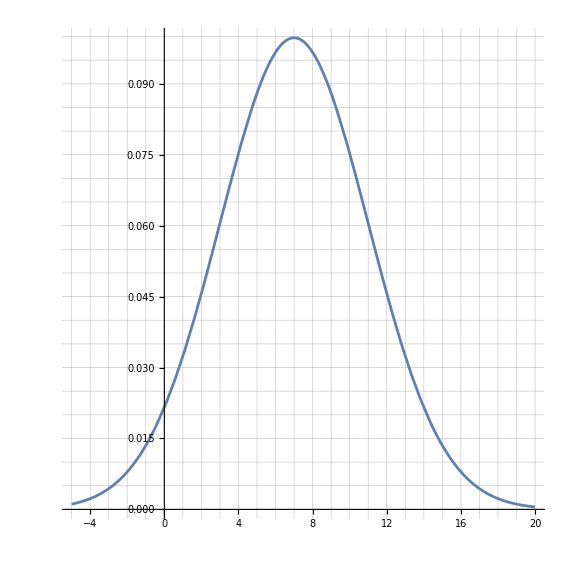

```mathematica
Plot[1/(√(2Pi)*4)Exp[-(x-7)^2/(2 *4^2)],{x, -5, 20}, GridLines->{Range[-5,20,1], Range[0,0.1,0.005]}, AspectRatio->1]
```